Take-up Calcs
We solve for takeup as a position of arm angles. We rename the variables to match the python variables. We then differentiate it for the statespace model.

```mathematica
LTakeupSide[a_,Larm_, dpdp_, dap_] := Sqrt[(Larm Cos[a] - dap)^2 + (Larm Sin[a])^2] + Sqrt[(dap + dpdp - Larm Cos[a])^2 + (Larm Sin[a])^2] - dpdp;
LTakeup[a_, b_, Larm_, dpdp_, dap_] := LTakeupSide[a,Larm, dpdp, dap] + LTakeupSide[b,Larm, dpdp, dap];
```

```mathematica
FullSimplify[LTakeup[Subscript[α, 1], Subscript[α, 2], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]]
```

-2 d_pdp+√(d_ap^2-2 Cos[α_1] d_ap L_arm+L_arm^2)+√(d_ap^2-2 Cos[α_2] d_ap L_arm+L_arm^2)+√((d_ap+d_pdp)^2-2 Cos[α_1] (d_ap+d_pdp) L_arm+L_arm^2)+√((d_ap+d_pdp)^2-2 Cos[α_2] (d_ap+d_pdp) L_arm+L_arm^2)

```mathematica
deriv = Dt[LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap}]
```

-2 Dt[dpdp]+(2 Larm Dt[Larm] Sin[a[t]]^2+2 Larm^2 Cos[a[t]] Dt[t] Sin[a[t]] a'[t]+2 (-dap+Larm Cos[a[t]]) (-Dt[dap]+Cos[a[t]] Dt[Larm]-Larm Dt[t] Sin[a[t]] a'[t]))/(2 √((-dap+Larm Cos[a[t]])^2+Larm^2 Sin[a[t]]^2))+(2 Larm Dt[Larm] Sin[a[t]]^2+2 Larm^2 Cos[a[t]] Dt[t] Sin[a[t]] a'[t]+2 (dap+dpdp-Larm Cos[a[t]]) (Dt[dap]+Dt[dpdp]-Cos[a[t]] Dt[Larm]+Larm Dt[t] Sin[a[t]] a'[t]))/(2 √((dap+dpdp-Larm Cos[a[t]])^2+Larm^2 Sin[a[t]]^2))+(2 Larm Dt[Larm] Sin[b[t]]^2+2 Larm^2 Cos[b[t]] Dt[t] Sin[b[t]] b'[t]+2 (-dap+Larm Cos[b[t]]) (-Dt[dap]+Cos[b[t]] Dt[Larm]-Larm Dt[t] Sin[b[t]] b'[t]))/(2 √((-dap+Larm Cos[b[t]])^2+Larm^2 Sin[b[t]]^2))+(2 Larm Dt[Larm] Sin[b[t]]^2+2 Larm^2 Cos[b[t]] Dt[t] Sin[b[t]] b'[t]+2 (dap+dpdp-Larm Cos[b[t]]) (Dt[dap]+Dt[dpdp]-Cos[b[t]] Dt[Larm]+Larm Dt[t] Sin[b[t]] b'[t]))/(2 √((dap+dpdp-Larm Cos[b[t]])^2+Larm^2 Sin[b[t]]^2))

```mathematica
{deriv/. {a'[t]-> u1, b'[t] -> u2, a[t] -> x1, b[t] -> x2, Dt[dap] -> 0, Dt[Larm] -> 0, Dt[dpdp] -> 0, Dt[t] -> 1}}
```

{(2 Larm^2 u1 Cos[x1] Sin[x1]+2 Larm u1 (dap+dpdp-Larm Cos[x1]) Sin[x1])/(2 √((dap+dpdp-Larm Cos[x1])^2+Larm^2 Sin[x1]^2))+(2 Larm^2 u1 Cos[x1] Sin[x1]-2 Larm u1 (-dap+Larm Cos[x1]) Sin[x1])/(2 √((-dap+Larm Cos[x1])^2+Larm^2 Sin[x1]^2))+(2 Larm^2 u2 Cos[x2] Sin[x2]+2 Larm u2 (dap+dpdp-Larm Cos[x2]) Sin[x2])/(2 √((dap+dpdp-Larm Cos[x2])^2+Larm^2 Sin[x2]^2))+(2 Larm^2 u2 Cos[x2] Sin[x2]-2 Larm u2 (-dap+Larm Cos[x2]) Sin[x2])/(2 √((-dap+Larm Cos[x2])^2+Larm^2 Sin[x2]^2))}

X and Y Position Derivation
We solve for x and y position as a function of takeup and length of cable traversed. We rename the variables so that its easier to plug it into the Python notebook. We then turn them into functions of time and take the derivative for the statespace model.

```mathematica
xysoln = Solve[{
Subscript[L, cxs] == Sqrt[Subscript[x, s]^2 + Y^2],
Subscript[L, c]== Sqrt[Subscript[x, s]^2 + Y^2] + Sqrt[(Subscript[L, cs] - Subscript[x, s])^2 + Y^2],
Subscript[x, s] ≥  0,
Y ≥ 0,
Subscript[L, cxs] ≤ Subscript[L, c],
Subscript[L, c] < Subscript[L, c0],
Subscript[L, c] > 0,
Subscript[L, cs] > 0
}, {Subscript[x, s], Y}, Reals]
```

{{x_s→ConditionalExpression[(-L_c^2+L_cs^2+2 L_c L_cxs)/(2 L_cs), ],Y→ConditionalExpression[√(L_cxs^2-((-L_c^2+L_cs^2+2 L_c L_cxs)^2)/(4 L_cs^2)), ]}}

```mathematica
Subscript[x, s][t] = {Subscript[x, s] /. xysoln}/.{Subscript[L, c]->lencable- takeup, Subscript[L, cxs]-> poscable, Subscript[L, cs]-> cablespan}
```

{{ConditionalExpression[(cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)/(2 cablespan), ]}}

```mathematica
Subscript[y, s][t] = {Y /. xysoln}/.{Subscript[L, c]->lencable- takeup, Subscript[L, cxs]-> poscable, Subscript[L, cs]-> cablespan}
```

{{ConditionalExpression[√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2)), ]}}

```mathematica
derivx = Dt[Subscript[x, s][t]] /. {Dt[cablespan] -> 0, Dt[lencable] -> 0}
```

{{ConditionalExpression[(2 (lencable-takeup) Dt[poscable]-2 poscable Dt[takeup]+2 (lencable-takeup) Dt[takeup])/(2 cablespan), ]}}

```mathematica
derivy = Dt[Subscript[y, s][t]]/. {Dt[cablespan] -> 0, Dt[lencable] -> 0}
```

{{ConditionalExpression[(2 poscable Dt[poscable]-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2) (2 (lencable-takeup) Dt[poscable]-2 poscable Dt[takeup]+2 (lencable-takeup) Dt[takeup]))/(2 cablespan^2))/(2 √(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2))), ]}}

```mathematica
derivx/.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3}
```

{{ConditionalExpression[(2 dx3 (lencable-x3)+2 u3 (lencable-x3)-2 dx3 x4)/(2 cablespan), ]}}

```mathematica
derivy /.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3}
```

{{ConditionalExpression[(2 u3 x4-((2 dx3 (lencable-x3)+2 u3 (lencable-x3)-2 dx3 x4) (cablespan^2-(lencable-x3)^2+2 (lencable-x3) x4))/(2 cablespan^2))/(2 √(x4^2-((cablespan^2-(lencable-x3)^2+2 (lencable-x3) x4)^2)/(4 cablespan^2))), ]}}

Tension Model Derivation
We solve for left and right tension as a function of x,y, takeup, and length of cable traversed. We rename the variables so that its easier to plug it into the Python notebook. We then turn them into functions of time and take the derivative for the statespace model.  We also solve for tension to help the model determine its initial states.

```mathematica
tensionsol = Solve[{Subscript[T, L] Subscript[x, s]/ Subscript[L, cxs] == Subscript[T, R](Subscript[L, cs] - Subscript[x, s])/(Subscript[L, c] - Subscript[L, cxs]),
Subscript[T, L] y/Subscript[L, cxs] + Subscript[T, R] y /(Subscript[L, c] - Subscript[L, cxs])== Subscript[m, s] g
} /. { Subscript[L, c]-> Subscript[L, c0] - Subscript[L, t]}, {Subscript[T, L], Subscript[T, R]}
]
```

{{T_L→(g L_cxs m_s (L_cs-x_s))/(y L_cs),T_R→-(-g L_c0 m_s x_s+g L_cxs m_s x_s+g L_t m_s x_s)/(y L_cs)}}

```mathematica
TL[t] = {Subscript[T, L]/.tensionsol}/. {Subscript[x, s] -> x[t], y -> y[t], Subscript[L, cxs]-> poscable, Subscript[m, s] -> mshuttle,  Subscript[L, cs]-> cablespan}
```

{{(g mshuttle poscable (cablespan-x[t]))/(cablespan y[t])}}

```mathematica
TR[t] = {Subscript[T, R]/.tensionsol}/. {Subscript[x, s] -> x[t], y -> y[t], Subscript[L, c0] -> lencable, Subscript[L, t]-> takeup, Subscript[L, cxs]-> poscable, Subscript[m, s] -> mshuttle,  Subscript[L, cs]-> cablespan}
```

{{-(-g lencable mshuttle x[t]+g mshuttle poscable x[t]+g mshuttle takeup x[t])/(cablespan y[t])}}

```mathematica
derivtl = Dt[TL[t]] /.{Dt[t] -> 1, Dt[cablespan] -> 0, Dt[g] -> 0, Dt[mshuttle] ->0}
```

{{(g mshuttle Dt[poscable] (cablespan-x[t]))/(cablespan y[t])-(g mshuttle poscable x'[t])/(cablespan y[t])-(g mshuttle poscable (cablespan-x[t]) y'[t])/(cablespan y[t]^2)}}

```mathematica
derivtr = Dt[TR[t]]/.{Dt[t] -> 1, Dt[cablespan] -> 0, Dt[g] -> 0, Dt[mshuttle] -> 0}
```

{{-1/(cablespan y[t])(-g mshuttle Dt[lencable] x[t]+g mshuttle Dt[poscable] x[t]+g mshuttle Dt[takeup] x[t]-g lencable mshuttle x'[t]+g mshuttle poscable x'[t]+g mshuttle takeup x'[t])+((-g lencable mshuttle x[t]+g mshuttle poscable x[t]+g mshuttle takeup x[t]) y'[t])/(cablespan y[t]^2)}}

```mathematica
derivtl/.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3, x[t] ->x5, y[t] -> x6, x'[t] -> dx5, y'[t]->dx6, Dt[t] -> 1}
```

{{-(dx6 g mshuttle x4 (cablespan-x5))/(cablespan x6^2)-(dx5 g mshuttle x4)/(cablespan x6)+(g mshuttle u3 (cablespan-x5))/(cablespan x6)}}

```mathematica
derivtr/.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3, x[t] ->x5, y[t] -> x6, x'[t] -> dx5, y'[t]->dx6, Dt[lencable] -> 0, Dt[t] -> 1}
```

{{(dx6 (-g lencable mshuttle x5+g mshuttle x3 x5+g mshuttle x4 x5))/(cablespan x6^2)-(-dx5 g lencable mshuttle+dx5 g mshuttle x3+dx5 g mshuttle x4+dx3 g mshuttle x5+g mshuttle u3 x5)/(cablespan x6)}}

```mathematica
FullSimplify[Solve[-(-g Subscript[L, c0] Subscript[m, s] Subscript[x, s]+g Subscript[L, cxs] Subscript[m, s] Subscript[x, s]+g Subscript[L, t] Subscript[m, s] Subscript[x, s])/(y Subscript[L, cs]) == Subscript[T, R], Subscript[L, t]]]/.{Subscript[L, c]->lencable- takeup, Subscript[L, cxs]-> poscable, Subscript[L, cs]-> cablespan, Subscript[T, R] -> tr, Subscript[m, s]-> mshuttle, Subscript[x, s]->x, Subscript[L, c0]-> lencable}
```

{{L_t→lencable-poscable-(cablespan tr y)/(g mshuttle x)}}

{{ConditionalExpression[√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2)), ]}}

```mathematica
{{√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2))}}
```

{{√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2))}}

```mathematica
TL[t]/.{x[t] -> x, y[t] -> y}
```

{{(g mshuttle poscable (cablespan-x))/(cablespan y)}}

```mathematica
TR[t] /.{x[t] -> x, y[t] -> y}
```

{{-(-g lencable mshuttle x+g mshuttle poscable x+g mshuttle takeup x)/(cablespan y)}}

Solve for angles to get required takeup
The first one is the case in which the arm angles are the same.
The second one is the case in which one arm is full raised and the other is fully lowered.

```mathematica
DoubleArmTakeup = Solve[{LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]} == mintakeup/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap, a[t] -> a, b[t] -> a}, a][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{a→ArcCos[1/(128 dpdp^2 Larm^2)(-Larm mintakeup (128 dap dpdp+64 dpdp^2+32 dap mintakeup+16 dpdp mintakeup)+√(Larm^2 mintakeup^2 (128 dap dpdp+64 dpdp^2+32 dap mintakeup+16 dpdp mintakeup)^2-256 dpdp^2 Larm^2 (-64 dpdp^2 Larm^2-64 dap^2 dpdp mintakeup-64 dap dpdp^2 mintakeup-64 dpdp Larm^2 mintakeup-16 dap^2 mintakeup^2-16 dap dpdp mintakeup^2+16 dpdp^2 mintakeup^2-16 Larm^2 mintakeup^2+8 dpdp mintakeup^3+mintakeup^4)))]}

```mathematica
SingleArmTakeup = Solve[{LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]} == mintakeup/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap, a[t] -> a, b[t] -> 0}, a][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{a→ArcCos[1/(8 dpdp^2 Larm^2)(-Larm (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3-32 dap dpdp √((dap-Larm)^2)-16 dpdp^2 √((dap-Larm)^2)-32 dap dpdp √((dap+dpdp-Larm)^2)-16 dpdp^2 √((dap+dpdp-Larm)^2)+16 dap √((dap-Larm)^2) √((dap+dpdp-Larm)^2)+8 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2)-32 dap^2 Larm-32 dap dpdp Larm-8 dpdp^2 Larm+16 dap Larm^2+8 dpdp Larm^2+32 dap dpdp mintakeup+16 dpdp^2 mintakeup-16 dap √((dap-Larm)^2) mintakeup-8 dpdp √((dap-Larm)^2) mintakeup-16 dap √((dap+dpdp-Larm)^2) mintakeup-8 dpdp √((dap+dpdp-Larm)^2) mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2)+√(Larm^2 (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3-32 dap dpdp √((dap-Larm)^2)-16 dpdp^2 √((dap-Larm)^2)-32 dap dpdp √((dap+dpdp-Larm)^2)-16 dpdp^2 √((dap+dpdp-Larm)^2)+16 dap √((dap-Larm)^2) √((dap+dpdp-Larm)^2)+8 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2)-32 dap^2 Larm-32 dap dpdp Larm-8 dpdp^2 Larm+16 dap Larm^2+8 dpdp Larm^2+32 dap dpdp mintakeup+16 dpdp^2 mintakeup-16 dap √((dap-Larm)^2) mintakeup-8 dpdp √((dap-Larm)^2) mintakeup-16 dap √((dap+dpdp-Larm)^2) mintakeup-8 dpdp √((dap+dpdp-Larm)^2) mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2)^2-16 dpdp^2 Larm^2 (32 dap^2 dpdp^2+32 dap dpdp^3+32 dpdp^4-16 dap^2 dpdp √((dap-Larm)^2)-32 dap dpdp^2 √((dap-Larm)^2)-48 dpdp^3 √((dap-Larm)^2)-16 dap^2 dpdp √((dap+dpdp-Larm)^2)-32 dpdp^3 √((dap+dpdp-Larm)^2)+48 dpdp^2 √((dap-Larm)^2) √((dap+dpdp-Larm)^2)-16 dap^3 Larm-24 dap^2 dpdp Larm-104 dap dpdp^2 Larm-48 dpdp^3 Larm+64 dap dpdp √((dap-Larm)^2) Larm+48 dpdp^2 √((dap-Larm)^2) Larm+64 dap dpdp √((dap+dpdp-Larm)^2) Larm+16 dpdp^2 √((dap+dpdp-Larm)^2) Larm-16 dap √((dap-Larm)^2) √((dap+dpdp-Larm)^2) Larm-8 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2) Larm+32 dap^2 Larm^2+32 dap dpdp Larm^2+36 dpdp^2 Larm^2-16 dpdp √((dap-Larm)^2) Larm^2-16 dpdp √((dap+dpdp-Larm)^2) Larm^2-16 dap Larm^3-8 dpdp Larm^3+32 dap^2 dpdp mintakeup+32 dap dpdp^2 mintakeup+48 dpdp^3 mintakeup-8 dap^2 √((dap-Larm)^2) mintakeup-16 dap dpdp √((dap-Larm)^2) mintakeup-56 dpdp^2 √((dap-Larm)^2) mintakeup-8 dap^2 √((dap+dpdp-Larm)^2) mintakeup-48 dpdp^2 √((dap+dpdp-Larm)^2) mintakeup+48 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2) mintakeup-96 dap dpdp Larm mintakeup-48 dpdp^2 Larm mintakeup+32 dap √((dap-Larm)^2) Larm mintakeup+24 dpdp √((dap-Larm)^2) Larm mintakeup+32 dap √((dap+dpdp-Larm)^2) Larm mintakeup+8 dpdp √((dap+dpdp-Larm)^2) Larm mintakeup+32 dpdp Larm^2 mintakeup-8 √((dap-Larm)^2) Larm^2 mintakeup-8 √((dap+dpdp-Larm)^2) Larm^2 mintakeup+8 dap^2 mintakeup^2+8 dap dpdp mintakeup^2+28 dpdp^2 mintakeup^2-24 dpdp √((dap-Larm)^2) mintakeup^2-24 dpdp √((dap+dpdp-Larm)^2) mintakeup^2+12 √((dap-Larm)^2) √((dap+dpdp-Larm)^2) mintakeup^2-24 dap Larm mintakeup^2-12 dpdp Larm mintakeup^2+8 Larm^2 mintakeup^2+8 dpdp mintakeup^3-4 √((dap-Larm)^2) mintakeup^3-4 √((dap+dpdp-Larm)^2) mintakeup^3+mintakeup^4)))]}

```mathematica
DetermineOtherAngle = Solve[{LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]} == mintakeup/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap, a[t] -> a, b[t] -> b}, a][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{a→ArcCos[1/(8 dpdp^2 Larm^2)(-Larm (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3+32 dap dpdp mintakeup+16 dpdp^2 mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2-32 dap^2 Larm Cos[b]-32 dap dpdp Larm Cos[b]-8 dpdp^2 Larm Cos[b]+16 dap Larm^2 Cos[b]^2+8 dpdp Larm^2 Cos[b]^2+16 dap Larm^2 Sin[b]^2+8 dpdp Larm^2 Sin[b]^2-32 dap dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dap dpdp √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dap √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2))+√(Larm^2 (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3+32 dap dpdp mintakeup+16 dpdp^2 mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2-32 dap^2 Larm Cos[b]-32 dap dpdp Larm Cos[b]-8 dpdp^2 Larm Cos[b]+16 dap Larm^2 Cos[b]^2+8 dpdp Larm^2 Cos[b]^2+16 dap Larm^2 Sin[b]^2+8 dpdp Larm^2 Sin[b]^2-32 dap dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dap dpdp √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dap √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2))^2-16 dpdp^2 Larm^2 (32 dap^2 dpdp^2+32 dap dpdp^3+32 dpdp^4-8 dap^2 Larm^2-8 dap dpdp Larm^2-20 dpdp^2 Larm^2+32 dap^2 dpdp mintakeup+32 dap dpdp^2 mintakeup+48 dpdp^3 mintakeup-16 dpdp Larm^2 mintakeup+8 dap^2 mintakeup^2+8 dap dpdp mintakeup^2+28 dpdp^2 mintakeup^2-4 Larm^2 mintakeup^2+8 dpdp mintakeup^3+mintakeup^4-16 dap^3 Larm Cos[b]-24 dap^2 dpdp Larm Cos[b]-104 dap dpdp^2 Larm Cos[b]-48 dpdp^3 Larm Cos[b]+16 dap Larm^3 Cos[b]+8 dpdp Larm^3 Cos[b]-96 dap dpdp Larm mintakeup Cos[b]-48 dpdp^2 Larm mintakeup Cos[b]-24 dap Larm mintakeup^2 Cos[b]-12 dpdp Larm mintakeup^2 Cos[b]+40 dap^2 Larm^2 Cos[b]^2+40 dap dpdp Larm^2 Cos[b]^2+56 dpdp^2 Larm^2 Cos[b]^2-8 Larm^4 Cos[b]^2+48 dpdp Larm^2 mintakeup Cos[b]^2+12 Larm^2 mintakeup^2 Cos[b]^2-32 dap Larm^3 Cos[b]^3-16 dpdp Larm^3 Cos[b]^3+8 Larm^4 Cos[b]^4+8 dap^2 Larm^2 Sin[b]^2+8 dap dpdp Larm^2 Sin[b]^2+52 dpdp^2 Larm^2 Sin[b]^2-8 Larm^4 Sin[b]^2+48 dpdp Larm^2 mintakeup Sin[b]^2+12 Larm^2 mintakeup^2 Sin[b]^2-32 dap Larm^3 Cos[b] Sin[b]^2-16 dpdp Larm^3 Cos[b] Sin[b]^2+16 Larm^4 Cos[b]^2 Sin[b]^2+8 Larm^4 Sin[b]^4-16 dap^2 dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dap dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-48 dpdp^3 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dpdp Larm^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dap^2 mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-56 dpdp^2 mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-24 dpdp mintakeup^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-4 mintakeup^3 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+64 dap dpdp Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+48 dpdp^2 Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+32 dap Larm mintakeup Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+24 dpdp Larm mintakeup Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Cos[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Cos[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Sin[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Sin[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap^2 dpdp √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp^3 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dpdp Larm^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dap^2 mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-48 dpdp^2 mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-24 dpdp mintakeup^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-4 mintakeup^3 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+64 dap dpdp Larm Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dpdp^2 Larm Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+32 dap Larm mintakeup Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 dpdp Larm mintakeup Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Cos[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Cos[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Sin[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Sin[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+48 dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 Larm^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+48 dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+12 mintakeup^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 Cos[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 Sin[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2))))]}

Results from the Math (These should be used to sanity check values and for implementing unit tests in code)

```mathematica
DoubleArmTakeup /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
DoubleArmTakeup /. {mintakeup -> 0.3, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
DoubleArmTakeup /. {mintakeup -> 0.2, Larm -> 0.125, dap -> 0.1, dpdp -> 0.5}
DoubleArmTakeup /. {mintakeup -> 0.98, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
DoubleArmTakeup /. {mintakeup -> 0.6, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
```

{a→0.702827}

{a→0.505545}

{a→0.743654}

{a→1.2852}

{a→0.842265}

```mathematica
SingleArmTakeup /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
SingleArmTakeup /. {mintakeup -> 0.3, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
SingleArmTakeup /. {mintakeup -> 0.2, Larm -> 0.125, dap -> 0.1, dpdp -> 0.5}
SingleArmTakeup /. {mintakeup -> 0.5, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
SingleArmTakeup /. {mintakeup -> 0.6, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
```

{a→1.24836}

{a→0.842265}

{a→1.22097}

{a→1.31002}

{a→1.57219}

```mathematica
DetermineOtherAngle /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 0.523}
DetermineOtherAngle /. {mintakeup -> 0.3, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 0.0}
DetermineOtherAngle /. {mintakeup -> 0.2, Larm -> 0.125, dap -> 0.1, dpdp -> 0.5, b-> 0.74365}
DetermineOtherAngle /. {mintakeup -> 0.5, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 1.31}
DetermineOtherAngle /. {mintakeup -> 0.6, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b->1}
```

{a→0.88133}

{a→0.842265}

{a→0.743657}

{a→0.0030547}

{a→0.686734}

```mathematica
LTakeup[0.702827,0.702827,0.25,0.1542, 0.2]
LTakeup[0.505545,0.505545,0.25,0.1542, 0.2]
LTakeup[1.31002,0,0.25,0.1542, 0.2]
LTakeup[1.57219,0.0,0.25,0.1542, 0.2]
LTakeup[0.0,1.57219,0.25,0.1542, 0.2]
```

0.475

0.3

0.499999

0.599999

0.599999

C++ Form: Puts out math into CPP Form so that we can paste it into code.

```mathematica
CForm[LTakeup[leftArmAngle, rightArmAngle, Larm, dpdp, dap]]
```

-2*dpdp + Sqrt(Power(dap + dpdp - Larm*Cos(leftArmAngle),2) + Power(Larm,2)*Power(Sin(leftArmAngle),2)) + 
   Sqrt(Power(-dap + Larm*Cos(leftArmAngle),2) + Power(Larm,2)*Power(Sin(leftArmAngle),2)) + 
   Sqrt(Power(dap + dpdp - Larm*Cos(rightArmAngle),2) + Power(Larm,2)*Power(Sin(rightArmAngle),2)) + 
   Sqrt(Power(-dap + Larm*Cos(rightArmAngle),2) + Power(Larm,2)*Power(Sin(rightArmAngle),2))

```mathematica
CForm[a /. DoubleArmTakeup]
```

ArcCos((-(Larm*mintakeup*(128*dap*dpdp + 64*Power(dpdp,2) + 32*dap*mintakeup + 16*dpdp*mintakeup)) + 
      Sqrt(Power(Larm,2)*Power(mintakeup,2)*Power(128*dap*dpdp + 64*Power(dpdp,2) + 32*dap*mintakeup + 16*dpdp*mintakeup,2) - 
        256*Power(dpdp,2)*Power(Larm,2)*(-64*Power(dpdp,2)*Power(Larm,2) - 64*Power(dap,2)*dpdp*mintakeup - 64*dap*Power(dpdp,2)*mintakeup - 64*dpdp*Power(Larm,2)*mintakeup - 
           16*Power(dap,2)*Power(mintakeup,2) - 16*dap*dpdp*Power(mintakeup,2) + 16*Power(dpdp,2)*Power(mintakeup,2) - 16*Power(Larm,2)*Power(mintakeup,2) + 
           8*dpdp*Power(mintakeup,3) + Power(mintakeup,4))))/(128.*Power(dpdp,2)*Power(Larm,2)))

```mathematica
CForm[a /. SingleArmTakeup]
```

ArcCos((-(Larm*(16*Power(dap,3) + 24*Power(dap,2)*dpdp + 40*dap*Power(dpdp,2) + 16*Power(dpdp,3) - 32*dap*dpdp*Sqrt(Power(dap - Larm,2)) - 
           16*Power(dpdp,2)*Sqrt(Power(dap - Larm,2)) - 32*dap*dpdp*Sqrt(Power(dap + dpdp - Larm,2)) - 16*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2)) + 
           16*dap*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) + 8*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) - 32*Power(dap,2)*Larm - 
           32*dap*dpdp*Larm - 8*Power(dpdp,2)*Larm + 16*dap*Power(Larm,2) + 8*dpdp*Power(Larm,2) + 32*dap*dpdp*mintakeup + 16*Power(dpdp,2)*mintakeup - 
           16*dap*Sqrt(Power(dap - Larm,2))*mintakeup - 8*dpdp*Sqrt(Power(dap - Larm,2))*mintakeup - 16*dap*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           8*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup + 8*dap*Power(mintakeup,2) + 4*dpdp*Power(mintakeup,2))) + 
      Sqrt(Power(Larm,2)*Power(16*Power(dap,3) + 24*Power(dap,2)*dpdp + 40*dap*Power(dpdp,2) + 16*Power(dpdp,3) - 32*dap*dpdp*Sqrt(Power(dap - Larm,2)) - 
           16*Power(dpdp,2)*Sqrt(Power(dap - Larm,2)) - 32*dap*dpdp*Sqrt(Power(dap + dpdp - Larm,2)) - 16*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2)) + 
           16*dap*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) + 8*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) - 32*Power(dap,2)*Larm - 
           32*dap*dpdp*Larm - 8*Power(dpdp,2)*Larm + 16*dap*Power(Larm,2) + 8*dpdp*Power(Larm,2) + 32*dap*dpdp*mintakeup + 16*Power(dpdp,2)*mintakeup - 
           16*dap*Sqrt(Power(dap - Larm,2))*mintakeup - 8*dpdp*Sqrt(Power(dap - Larm,2))*mintakeup - 16*dap*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           8*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup + 8*dap*Power(mintakeup,2) + 4*dpdp*Power(mintakeup,2),2) - 
        16*Power(dpdp,2)*Power(Larm,2)*(32*Power(dap,2)*Power(dpdp,2) + 32*dap*Power(dpdp,3) + 32*Power(dpdp,4) - 16*Power(dap,2)*dpdp*Sqrt(Power(dap - Larm,2)) - 
           32*dap*Power(dpdp,2)*Sqrt(Power(dap - Larm,2)) - 48*Power(dpdp,3)*Sqrt(Power(dap - Larm,2)) - 16*Power(dap,2)*dpdp*Sqrt(Power(dap + dpdp - Larm,2)) - 
           32*Power(dpdp,3)*Sqrt(Power(dap + dpdp - Larm,2)) + 48*Power(dpdp,2)*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) - 16*Power(dap,3)*Larm - 
           24*Power(dap,2)*dpdp*Larm - 104*dap*Power(dpdp,2)*Larm - 48*Power(dpdp,3)*Larm + 64*dap*dpdp*Sqrt(Power(dap - Larm,2))*Larm + 
           48*Power(dpdp,2)*Sqrt(Power(dap - Larm,2))*Larm + 64*dap*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Larm + 16*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2))*Larm - 
           16*dap*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*Larm - 8*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*Larm + 
           32*Power(dap,2)*Power(Larm,2) + 32*dap*dpdp*Power(Larm,2) + 36*Power(dpdp,2)*Power(Larm,2) - 16*dpdp*Sqrt(Power(dap - Larm,2))*Power(Larm,2) - 
           16*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Power(Larm,2) - 16*dap*Power(Larm,3) - 8*dpdp*Power(Larm,3) + 32*Power(dap,2)*dpdp*mintakeup + 
           32*dap*Power(dpdp,2)*mintakeup + 48*Power(dpdp,3)*mintakeup - 8*Power(dap,2)*Sqrt(Power(dap - Larm,2))*mintakeup - 16*dap*dpdp*Sqrt(Power(dap - Larm,2))*mintakeup - 
           56*Power(dpdp,2)*Sqrt(Power(dap - Larm,2))*mintakeup - 8*Power(dap,2)*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           48*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup + 48*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           96*dap*dpdp*Larm*mintakeup - 48*Power(dpdp,2)*Larm*mintakeup + 32*dap*Sqrt(Power(dap - Larm,2))*Larm*mintakeup + 24*dpdp*Sqrt(Power(dap - Larm,2))*Larm*mintakeup + 
           32*dap*Sqrt(Power(dap + dpdp - Larm,2))*Larm*mintakeup + 8*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Larm*mintakeup + 32*dpdp*Power(Larm,2)*mintakeup - 
           8*Sqrt(Power(dap - Larm,2))*Power(Larm,2)*mintakeup - 8*Sqrt(Power(dap + dpdp - Larm,2))*Power(Larm,2)*mintakeup + 8*Power(dap,2)*Power(mintakeup,2) + 
           8*dap*dpdp*Power(mintakeup,2) + 28*Power(dpdp,2)*Power(mintakeup,2) - 24*dpdp*Sqrt(Power(dap - Larm,2))*Power(mintakeup,2) - 
           24*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Power(mintakeup,2) + 12*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*Power(mintakeup,2) - 
           24*dap*Larm*Power(mintakeup,2) - 12*dpdp*Larm*Power(mintakeup,2) + 8*Power(Larm,2)*Power(mintakeup,2) + 8*dpdp*Power(mintakeup,3) - 
           4*Sqrt(Power(dap - Larm,2))*Power(mintakeup,3) - 4*Sqrt(Power(dap + dpdp - Larm,2))*Power(mintakeup,3) + Power(mintakeup,4))))/(8.*Power(dpdp,2)*Power(Larm,2)))

```mathematica
CForm[a /. (FullSimplify[DetermineOtherAngle] /. {b -> otherAngle})]
```

ArcCos((-((2*dap + dpdp)*Larm*(2*Power(dap,2) + 2*dap*dpdp + 2*Power(Larm,2) + Power(2*dpdp + mintakeup,2))) + 
      2*(2*dap + dpdp)*Larm*((2*dap + dpdp)*Larm*Cos(otherAngle) + mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
         mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
         Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
         2*dpdp*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
      2*Sqrt(Power(Larm,2)*(8*Power(dap,6) + 24*Power(dap,5)*dpdp + 2*Power(dap,4)*
            (37*Power(dpdp,2) + 16*Power(Larm,2) + 24*dpdp*mintakeup + 6*Power(mintakeup,2) + 
              4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
              16*dpdp*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              8*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
           Power(dpdp,2)*Power(Larm,2)*(5*Power(dpdp,2) + 2*Power(Larm,2) + Power(mintakeup,2) + 
              2*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
              2*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              4*dpdp*(-mintakeup + Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
           4*Power(dap,3)*dpdp*(27*Power(dpdp,2) + 16*Power(Larm,2) + 6*Power(mintakeup,2) - 10*mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) - 
              6*mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
              4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
              4*dpdp*(-6*mintakeup + 5*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 3*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
           dap*dpdp*(36*Power(dpdp,4) + 8*Power(Larm,4) - 4*Power(dpdp,3)*
               (-13*mintakeup + 13*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 9*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) + 
              Power(dpdp,2)*(58*Power(Larm,2) + 29*Power(mintakeup,2) - 58*mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) - 
                 50*mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
                 50*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              8*dpdp*Power(Larm,2)*(-6*mintakeup + 4*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
              4*Power(Larm,2)*(3*Power(mintakeup,2) + 2*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + Power(mintakeup,2)*(Power(mintakeup,2) + 12*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + 8*dpdp*mintakeup*(Power(mintakeup,2) + 6*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 3*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
              ) + Power(dap,2)*(86*Power(dpdp,4) + 8*Power(Larm,4) - 4*Power(dpdp,3)*
               (-25*mintakeup + 25*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 13*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) + 
              Power(dpdp,2)*(90*Power(Larm,2) + 41*Power(mintakeup,2) - 82*mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) - 
                 58*mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
                 58*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              8*dpdp*Power(Larm,2)*(-6*mintakeup + 4*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
              4*Power(Larm,2)*(3*Power(mintakeup,2) + 2*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + Power(mintakeup,2)*(Power(mintakeup,2) + 12*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + 8*dpdp*mintakeup*(Power(mintakeup,2) + 6*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 3*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
              ) + 2*Larm*Cos(otherAngle)*(-16*Power(dap,5) - 40*Power(dap,4)*dpdp - Power(dpdp,3)*Power(Larm,2) - 
              2*Power(dap,3)*(41*Power(dpdp,2) + 8*Power(Larm,2) + 24*dpdp*mintakeup + 6*Power(mintakeup,2) + 
                 4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 16*dpdp*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
                 8*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + dap*Power(dpdp,2)*(-25*Power(dpdp,2) - 10*Power(Larm,2) - 6*Power(mintakeup,2) - 
                 4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
                 4*mintakeup*(3*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) + 
                 8*dpdp*(-3*mintakeup + 3*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
              Power(dap,2)*dpdp*(-83*Power(dpdp,2) + 8*dpdp*(-9*mintakeup + 7*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    5*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
                 2*(12*Power(Larm,2) + 9*Power(mintakeup,2) + 6*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                     Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                    2*mintakeup*(7*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                       5*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))))) + 
           2*dap*(dap + dpdp)*(8*Power(dap,2) + 8*dap*dpdp + Power(dpdp,2))*Power(Larm,2)*Cos(2*otherAngle))))/(2.*Power(dpdp,2)*Power(Larm,2)))

```mathematica
a * 180 / Pi/.{DetermineOtherAngle /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 0 * Pi/180}}
```

{71.5256}

Plotting Arm Transition level sets

This helps us understand the relative motion of the arms to maintain constant tension.

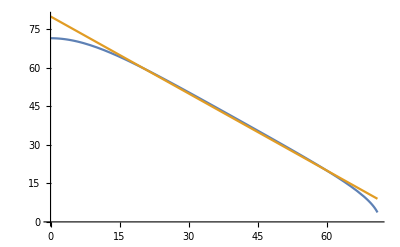

```mathematica
Plot[{a* 180 / Pi/.{DetermineOtherAngle /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> bscaled * Pi/180}}, 80 - bscaled}, {bscaled, 0, 71}]
```

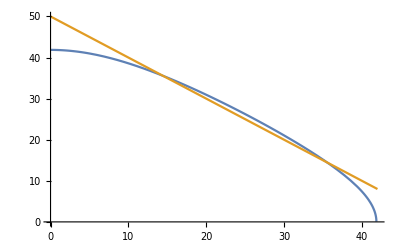

```mathematica
Plot[{a* 180 / Pi/.{DetermineOtherAngle /. {mintakeup -> 0.25, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> bscaled * Pi/180}}, 50 - bscaled}, {bscaled, 0, 42}]
```